```mathematica
SetDirectory["/Users/kuzubatomohiko/Documents/M1/多変量解析/樹木データ"]
```

/Users/kuzubatomohiko/Documents/M1/多変量解析/樹木データ

```mathematica
１３種類の胴回りの寸法　、重さ、高さ　４年のタイミング１５年立った時のタイミング
胴回りから重量を推定したいというモチベーション
縦断的な研究、横断的
 root-stock    木ごとの個体　一本目の木、二本目の木〜１３こ
104
```

、^2 重さ 高さ １３種類の胴回りの寸法 ４年のタイミング１５年立った時のタイミング

胴回りから重量を推定したいというモチベーション

、 横断的 縦断的な研究

、 二本目の木〜１３こ (root-一本目の木 木ごとの個体 stock)

104

```mathematica
data0=Import["Classical_Apple_Experiment.csv"];
```

```mathematica
data1=Transpose[data0[[1]]];
```

Transpose::nmtx: {I,111,2569,358,760}の最初の2個のレベルは転置できません．

```mathematica
x=data1[[4]];
y=data1[[5]];
```

Part::partw: Transpose[{I,111,2569,358,760}]の部分4は存在しません．

Part::partw: Transpose[{I,111,2569,358,760}]の部分5は存在しません．

```mathematica
data=Transpose[{x,y}];
data//MatrixForm
```

Transpose::nmtx: {Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}の最初の2個のレベルは転置できません．

Transpose[{Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}]

```mathematica
sp=ListPlot[data,AspectRatio->1,AxesLabel->{"x(mm)","y(lb)"},AxesOrigin->{0,0}]
縦軸はポンドになっている->重量
横軸はmm ->cm
```

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分5は存在しません．

Transpose::nmtx: {Transpose[{I,111.,2569.,358.,760.}]⟦4⟧,Transpose[{I,111.,2569.,358.,760.}]⟦5⟧}の最初の2個のレベルは転置できません．

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

ListPlot::lpn: Transpose[{Transpose[{I,111.,2569.,358.,760.}]⟦4⟧,Transpose[{I,111.,2569.,358.,760.}]⟦5⟧}]は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[Transpose[{Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}],AspectRatio→1,AxesLabel→{x(mm),y(lb)},AxesOrigin→{0,0}]

縦軸はポンドになっている→重量

横軸はmm→cm

```mathematica
model3=β0+β1 x+β2 x^2;
```

```mathematica
ϵ3[β0_,β1_,β2_]:=Total[(y-(β0+β1 x+β2 x^2))^2]
```

```mathematica
FindMinimum[{ϵ3[β0,β1,β2]},{β0,β1,β2}]
```

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分5は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

FindMinimum::nrnum: 関数の値Total[(-1.-1. Transpose[{I,111,2569,358,760}]⟦4⟧-1. (Transpose[{«5»}]⟦4⟧)^2+Transpose[{I,111,2569,358,760}]⟦5⟧)^2]は{β0,β1,β2} = {1.,1.,1.}において実数ではありません．

FindMinimum[{ϵ3[β0,β1,β2]},{β0,β1,β2}]

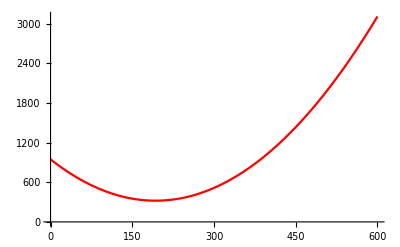

```mathematica
p3=Plot[946.86-6.4889 x +0.016827 x^2,{x,0,600},AxesOrigin->{0,0},PlotStyle->Red]
```

```mathematica
Show[sp,p3]
```

Show::gcomb: Show[ListPlot[Transpose[{Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}],AspectRatio→1,AxesLabel→{x(mm),y(lb)},AxesOrigin→{0,0}],]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[ListPlot[Transpose[{Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}],AspectRatio→1,AxesLabel→{x(mm),y(lb)},AxesOrigin→{0,0}],-Graphics-]

```mathematica
model4=β0+β1 x+β2 x^2+β3 x^3;
```

```mathematica
ϵ4[β0_,β1_,β2_,β3_]:=Total[(y-(β0+β1 x+β2 x^2+β3 x^3))^2]
```

```mathematica
FindMinimum[{ϵ4[β0,β1,β2,β3]},{β0,β1,β2,β3}]
```

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

FindMinimum::nrnum: 関数の値Total[(-1.-1. Transpose[{I,111,2569,358,760}]⟦4⟧-1. (Transpose[{«5»}]⟦4⟧)^2-1. (Transpose[{«5»}]⟦4⟧)^3+Transpose[{I,111,2569,358,760}]⟦5⟧)^2]は{β0,β1,β2,β3} = {1.,1.,1.,1.}において実数ではありません．

FindMinimum[{ϵ4[β0,β1,β2,β3]},{β0,β1,β2,β3}]

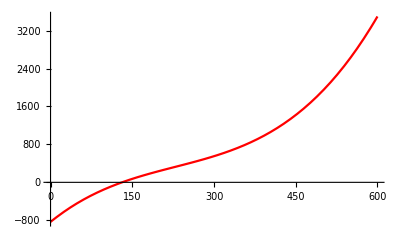

```mathematica
p4=Plot[-834.11+9.3072 x -0.027785 x^2+0.000040510 x^3,{x,0,600},AxesOrigin->{0,0},PlotStyle->Red]
```

```mathematica
Show[p4,sp]
```

Show::gcomb: Show[,ListPlot[Transpose[{Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}],AspectRatio→1,AxesLabel→{x(mm),y(lb)},AxesOrigin→{0,0}]]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[-Graphics-,ListPlot[Transpose[{Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}],AspectRatio→1,AxesLabel→{x(mm),y(lb)},AxesOrigin→{0,0}]]

```mathematica
modelexp=β0  Exp[β1 x];
```

```mathematica
ϵexp[β0_,β1_]:=Total[(y-(β0 Exp[β1 x]))^2]
```

```mathematica
FindMinimum[{ϵexp[β0,β1]},{β0,{β1,0}}]
```

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分4は存在しません．

Transpose::nmtx: {I,111.,2569.,358.,760.}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Part::partw: Transpose[{I,111.,2569.,358.,760.}]の部分5は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

FindMinimum::nrnum: 関数の値Total[(-1.+Transpose[{I,111,2569,358,760}]⟦5⟧)^2]は{β0,β1} = {1.,0.}において実数ではありません．

FindMinimum[{ϵexp[β0,β1]},{β0,{β1,0}}]

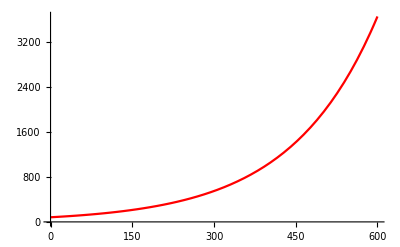

```mathematica
pexp=Plot[82.5085 ⅇ^(0.0063189 x),{x,0,600},AxesOrigin->{0,0},PlotStyle->Red]
```

```mathematica
Show[sp,pexp]
```

Show::gcomb: Show[ListPlot[Transpose[{Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}],AspectRatio→1,AxesLabel→{x(mm),y(lb)},AxesOrigin→{0,0}],]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[ListPlot[Transpose[{Transpose[{I,111,2569,358,760}]⟦4⟧,Transpose[{I,111,2569,358,760}]⟦5⟧}],AspectRatio→1,AxesLabel→{x(mm),y(lb)},AxesOrigin→{0,0}],-Graphics-]